Import the csv titled "Top_Sales_By_Customer-2.csv"

```mathematica
data=Import["Top_Sales_By_Customer-2.csv"]
```

How to run a cell and not show the output

Had trouble finding file, I'm using a mac and it's in my downloads folder, my username is erichegonzales

```mathematica
bigdata=Import["/Users/erichegonzales/Downloads/Top_Sales_By_Customer-3.csv"];
```

```mathematica
Length[bigdata]
```

10001

Graph this data

```mathematica
salesData=Rest[data];
sales=ToExpression[StringReplace[salesData[[All,1]],"$"->""]];
customers=salesData[[All,2]];

BarChart[sales,ChartLabels->customers,ImageSize->500,
PlotLabel->"Top Sales by Customer"]
```

seems to be an issue with the To Expression

```mathematica
salesData=Rest[bigdata];
sales=ToExpression[StringReplace[salesData[[All,1]],{","->"","$"->""}]];
```

```mathematica
customers=salesData[[All,2]];

BarChart[sales,ImageSize->500,
PlotLabel->"Top Sales by Customer"]
```

```mathematica
customersTiny = Style[#, Tiny]&/@ customers[[;;100]]
```

{PS 158,KidPass,Elizabeth Mangan,Manhattan Schoolhouse,St. Ignatius Loyola Day Nursery,Lilach Wasserman,Dominick Petruccelli,Jessica Chestman,Christopher Daly,ANUPAMA POOLE,Stacey Cohen,Julie Karen,Erin Eizenstat,Kim Klimczak,Greg Bulishak,Jaime Benjamin,Jeanne Peldman,Jessica Singer,Jenny Kees,Emily Rittberg,Shaaray Tefila,Maneesha Kacker,Melanie Sher,Marissa Senzon,Jenifer Geller,Lauren Ruderfer,David Yeung,Naomi Moss,Barbara O'Connor,Erin Schiffman,Veronica Santos,Jenna Kahn,Denise Folise,Jennifer Bhuta,Lana Saferstein,Kelly Meyers,David Pettker,Sherrie Soleymani,Stephanie Berk,Mary Miele,Meredith Barnett,Amie Munk,Sal Karakaplan,Randi Siegal,Maria Panganiban,Sylvia Rutherford,Abby Carey,Gina Argento,Ashley Buterman,Leslie Venokur,Chana Cohen,Natalia Edelson,Jennifer Radin,Marcie Pantzer,Daniella Gotlib,Carrie Schein,Joanna Goldman,Michelle Brill,Heidi Farrell,Melitza Lev,Deana Thomas,Carrie Cohen,Allison Marx,Lauren Erbst,Janine Hoffman,Audrey Goldstein,Hakan Altintepe,Park Children's Day School,Ariel Boyman,Abby Kaufthal,Durre Nabi,Park Avenue Synagogue (ECC),Super Soccer Stars,Izzet Bensusan,Marnie Nussbaum,Dana Kesselman,Dawn Darringer,Hillary Sherman,Rachel Mandell,Karen Fine,Elizabeth Keizner,Kate Bellin,Nicole Meyer,Kathleen Yeo,Stephanie Von Spiegel,Jennifer Dunn,Randi Sultan,Stephanie Hessler,Lindsay Schwartz,Andrew Colosimo,Allison Sassower,Marcelo Takieddine,Sally Mahloudji,Stacy Westreich,Wade Hooker,Joshua Alper,Stephanie Wagner,Jennifer Rubinstein,Manisha Jain,Marcy Czeizler}

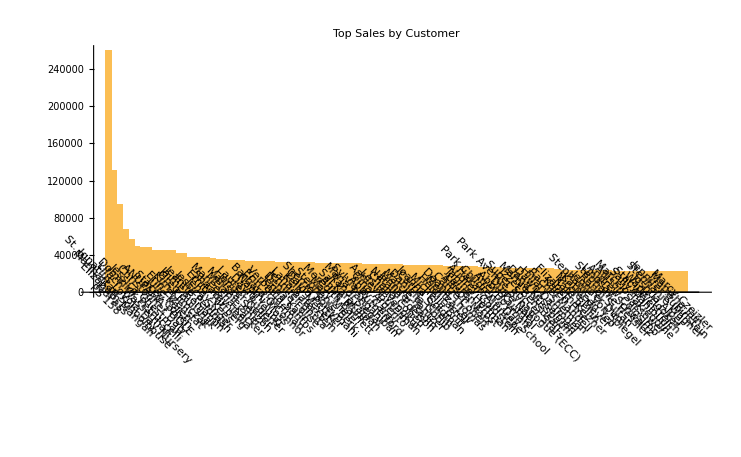

```mathematica
BarChart[sales[[;;100]],ImageSize->500,PlotLabel->"Top Sales by Customer", ChartLabels->Placed[customersTiny, Below, Rotate[#, -Pi/4]&]]
```

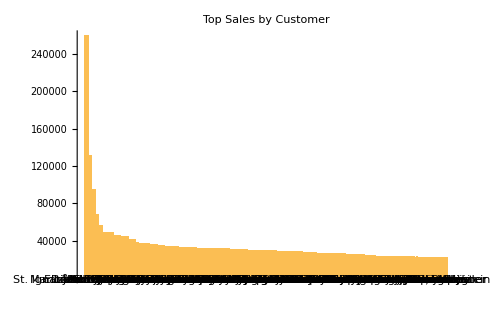

```mathematica
BarChart[MapThread[Labeled[#1,#2]&, {sales[[;;100]], customers[[;;100]]}],ImageSize->500,PlotLabel->"Top Sales by Customer"]
```

The hover is working but it's showing me every single value, I only want it to show the one I'm hovering over

```mathematica
BarChart[Take[sales,{250, 500}],ChartLabels->Placed[customers[[250;; 500]],Tooltip],ImageSize->500,PlotLabel->"Top Sales by Customer"]
```

Now show me in scatter plot form on a log log scale

```mathematica
ListLogLogPlot[sales,PlotStyle->PointSize[0.02],ImageSize->500,PlotLabel->"Top Sales by Customer"]
```

Show the line of best fit for this graph

```mathematica
fit=LinearModelFit[Transpose[{Range[Length[sales]],sales}],x,x];
line=fit["BestFit"];
Show[
  ListLogLogPlot[sales,PlotStyle->PointSize[0.02],ImageSize->500,PlotLabel->"Top Sales by Customer"],
  LogLogPlot[line,{x,1,Length[sales]},PlotStyle->Red]
]
```

This line is not straight, I want it to be straight

```mathematica
fit=LinearModelFit[Log[sales],x,x];
line=fit["BestFit"];

Show[
  ListLogLogPlot[sales,PlotStyle->PointSize[0.02],ImageSize->500,PlotLabel->"Top Sales by Customer"],
  LogLogPlot[line,{x,1,Length[sales]},PlotStyle->Red]
]
```

There is no line showing up now...

```mathematica
fit=LinearModelFit[Transpose[{Range[Length[sales]],Log[sales]}],x,x];
line=fit["BestFit"];

Show[
  ListLogLogPlot[sales,PlotStyle->PointSize[0.02],ImageSize->500,PlotLabel->"Top Sales by Customer"],
  LogLogPlot[Exp[line],{x,1,Length[sales]},PlotStyle->Red]
]
```

```mathematica
Mean[sales]
```

Get a list of 500 random values from the normal distribution with a mean of 18,571

```mathematica
randomValues=RandomVariate[NormalDistribution[18571,1],500]
```

sort the values from largest to smalles

```mathematica
sortedValues=Sort[randomValues,Greater]
```

Plot the random values on a log log plot

sort

```mathematica
ListLogLogPlot[sortedValues,PlotStyle->PointSize[0.02],ImageSize->500,PlotLabel->"Random Values"]
```

Now create 500 random values from the pareto distribution with a mean of 18,571